# 中子星的流体静力学平衡

## 流体静力学平衡方程：，这条方程是描述一个面元受到的压力与中心引力的平衡； 我们还需要知道随半径的分布：； 这里我们将物态方程写为多方幂函数的形式：，为多方指数，K为系数。

```mathematica
(*多方指数*)
P[r_]:=K ρ[r]^γ;

(*平衡方程*)
eq=D[P[r],r]==-G*Mr[r]*ρ[r]/r^2
```

K γ ρ[r]^(-1+γ) ρ'[r]==-(G Mr[r] ρ[r])/r^2

简化上式

```mathematica
rhoPrime=Solve[eq,ρ'[r]]//First//Simplify
```

{ρ'[r]→-(G Mr[r] ρ[r]^(2-γ))/(K r^2 γ)}

令γ = 1 + 1/n

```mathematica
γ := 1+ 1/n;
rhoPrime
```

{ρ'[r]→-(G Mr[r] ρ[r]^(1-1/n))/(K (1+1/n) r^2)}

令，ϕ满足

```mathematica
(*g[r_]:=ϕ[r]'; 和下一行等价*)
g[r_]:=ϕ'[r];
rhoPrime = rhoPrime/. G*Mr[r_]/r_^2:>g[r]
```

{ρ'[r]→-(ρ[r]^(1-1/n) ϕ'[r])/(K (1+1/n))}

### 我们想得到ρ[ϕ]

```mathematica
(*把rhoPrime由一个替换规则变成一条方程*)
rhoPrime=rhoPrime[[1]]/. Rule->Equal
```

ρ'[r]==-(ρ[r]^(1-1/n) ϕ'[r])/(K (1+1/n))

```mathematica
eq=rhoPrime/. {ρ[r]->ρ[ϕ],ρ'[r]->(D[ρ[ϕ],ϕ] ϕ'[r])}
```

ρ'[ϕ] ϕ'[r]==-(ρ[ϕ]^(1-1/n) ϕ'[r])/(K (1+1/n))

```mathematica
eqRhoPhi=Cancel[eq/ϕ'[r]]//Simplify
```

(((n ρ[ϕ]^(1-1/n))/(K+K n)+ρ'[ϕ]) ϕ'[r]==0)/ϕ'[r]

```mathematica
(*如果没有不等于0的假设就不会在形式上除掉，如上式*)
eqRhoPhi=Simplify[DivideSides[eq,ϕ'[r]],Assumptions->ϕ'[r]!=0]
```

(n ρ[ϕ]^(1-1/n))/(K+K n)+ρ'[ϕ]==0

求解函数ρ[ϕ]

```mathematica
rhophi=DSolve[eqRhoPhi,ρ,ϕ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ→Function[{ϕ},(-((n ϕ)/(K (1+n))-C[1])/n)^n]}}

我们取C1为0，即ρ[ϕ = 0] = 0

```mathematica
rhophi = rhophi /. C[1] -> 0
```

{{ρ→Function[{ϕ},(-((n ϕ)/(K (1+n))-0)/n)^n]}}

```mathematica
rhophieq=ρ[ϕ]->(rhophi[[1,1,2]][ϕ[r]])
```

ρ[ϕ]→(-ϕ[r]/(K (1+n)))^n

```mathematica
rhophieq
D[rhophieq,ϕ]
```

ρ[ϕ]→(-ϕ[r]/(K (1+n)))^n

ρ'[ϕ]→0

由于ρ满足，将代入这条式子
（考虑为球对称的只有r变量）

```mathematica
poisson=(1/r^2) D[r^2 ϕ'[r],r]==4 π G ρ[ϕ];
poissoneq=poisson /. rhophieq
```

(2 r ϕ'[r]+r^2 ϕ''[r])/r^2==4 G π (-ϕ[r]/(K (1+n)))^n

## Lane - Emden 方程

利用下列关系替换 、   、

```mathematica
(*1. 定义 z=A r 的替换规则*)
rRule=r-> z / A;  (*左边的换成右边的*)

(*2. ϕ(r)->ϕc ω(z)*)
phiRule=ϕ[r]->ϕc * ω[z];

(*3. 导数替换规则*)
drRule={ϕ'[r]->A * ϕc * D[ω[z],z],ϕ''[r]->A^2 * ϕc * D[ω[z],{z,2}]};

(*4. A^2*)
Arule1= A^2 -> (4 π G/(K*(1+n))^n) (- ϕc)^(n-1);

(*4. 把所有规则代入泊松方程*)
LEeq=poissoneq/. phiRule/. drRule/. rRule /. Arule1 /. phiRule;   (*从左到右运用*)

(*5. 化简*)
LEeq=FullSimplify[LEeq, {z>0,  G*(K*(1+n))^(-n)*(-ϕc)^n !=0, ω[z]!=0}]
```

z (-(ϕc ω[z])/(K+K n))^n+(K (1+n))^-n (-ϕc)^n (2 ω'[z]+z ω''[z])==0

由于共同项复杂难以用Simplify直接约去，花了2小时还是无法约去

```mathematica
common := x;
LEeq2 = LEeq /. (K (1+n))^-n (-ϕc)^n  :> common
```

z (-(ϕc ω[z])/(K+K n))^n+x (2 ω'[z]+z ω''[z])==0

```mathematica
common1 := x * ω[z]^n;
LEeq3 = LEeq2 /. (-ϕc ω[z]/(K +K n))^n  :> common1
```

x z ω[z]^n+x (2 ω'[z]+z ω''[z])==0

```mathematica
LEeqfinal = FullSimplify[LEeq3, {z>0,  x > 0}]
```

2 ω'[z]+z (ω[z]^n+ω''[z])==0

得到了Lane - Emden方程

```mathematica
Rhoeq = ρ[r_] == ρc ω[r];
Peq      = P[r_] == Pc ω[r]^(1+1/n);
Teq      = T[r_] == Tc ω[r]^(1/n);
z == Ar;
```

## 下面解这个方程组

```mathematica
n=1;  (*多方指数，可改*)

(*Lane–Emden 方程*)
LEeq=ω''[z]+(2/z) ω'[z]+ω[z]^n==0;

(*初值条件：避免 z=0 奇点，从很小的 ϵ 开始*)
ϵ=10^-10;

ics={ω[ϵ]==1-(1/6) ϵ^2,(*ω(0)=1 的二阶展开*)ω'[ϵ]==-(1/3) ϵ       (*ω'(0)=0 的一阶展开*)};

(*数值求解*)
sol=NDSolve[{LEeq,ics},ω,{z,ϵ,20},MaxSteps->Infinity];
```

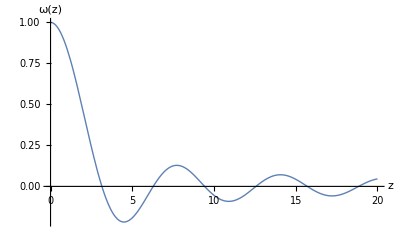

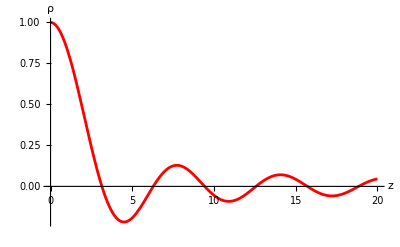

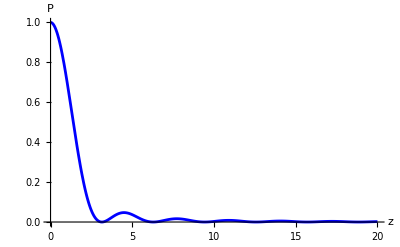

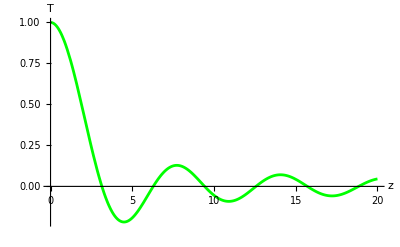

```mathematica
Plot[Evaluate[ω[z]/. sol],{z,0,20},PlotRange->All,AxesLabel->{"z","ω(z)"},PlotStyle->Thick]

ρplot=Plot[ρc ω[z]/. sol/. ρc->1,{z,0,20},PlotRange->All,PlotStyle->Red,AxesLabel->{"z","ρ"}]

Pplot=Plot[Pc (ω[z]/. sol)^(1+1/n)/. Pc->1,{z,0,20},PlotRange->All,PlotStyle->Blue,AxesLabel->{"z","P"}]

Tplot=Plot[Tc (ω[z]/. sol)^(1/n)/. Tc->1,{z,0,20},PlotRange->All,PlotStyle->Green,AxesLabel->{"z","T"}]
```

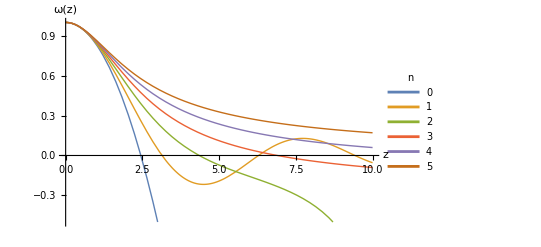

```mathematica
(*想画的 n 列表*)
nList={0,1,2,3,4,5};

ϵ=10^-10; (*初值*)

(*定义一个函数：给定 n，返回 ω(z) 的数值解*)
solveLE[n_]:=Module[{LEeq,ics,sol},LEeq=ω''[z]+(2/z) ω'[z]+ω[z]^n==0;
ics={ω[ϵ]==1-(1/6) ϵ^2,ω'[ϵ]==-(1/3) ϵ};
sol=NDSolve[{LEeq,ics},ω,{z,ϵ,10},MaxSteps->Infinity];
sol];

(*求所有 n 的解*)
solList=Table[{n,solveLE[n]},{n,nList}];

(*绘图*)
Plot[Evaluate[Table[ω[z]/. solList[[i,2]],{i,Length[nList]}]],{z,0,10},PlotRange->{-0.5,1},PlotStyle->Thick,AxesLabel->{"z","ω(z)"},PlotLegends->Placed[LineLegend[nList,LegendLabel->"n"],Right]]
```

### 到这里一共花了9小时，结果与[“https://en.wikipedia.org/wiki/Lane%E2%80%93Emden_equation”]中的图1一模一样